## Sin[x] のTaylor展開

### y = Sin[x] のグラフ

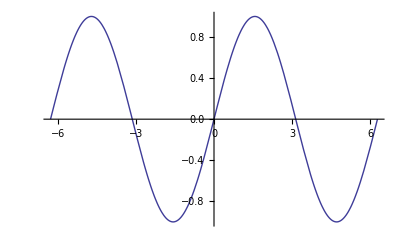

```mathematica
Plot[Sin[x],{x,-2Pi,2Pi}]
```

### Sin[x] を x=0 を中心に5乗の項までテイラー展開

```mathematica
Series[Sin[x],{x,0,5}]
```

x-x^3/6+x^5/120+O[x]^6

### y = Sin[x] とテイラー展開した級数とのグラフのちがい

```mathematica
Manipulate[
Plot[{Sin[x],Normal[Series[Sin[y],{y,0,n}]]/.y->x},{x,-3Pi,3Pi},
PlotRange->{{-10,10},{-3,3}}],
{n,1,25,2}]
```

## Log[x] のTaylor展開

### y = Log[x] のグラフ

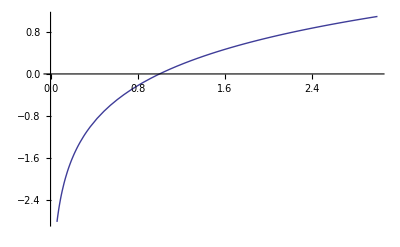

```mathematica
Plot[Log[x],{x,0,3}]
```

### Log[x] を x=1 を中心に5乗の項までテイラー展開

```mathematica
Series[Log[x],{x,1,5}]
```

(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5+O[x-1]^6

### y = Log[x] とテイラー展開した級数とのグラフのちがい

```mathematica
Manipulate[
Plot[{Log[x],Normal[Series[Log[y],{y,1,n}]]/.y->x},{x,0,3},
PlotRange->{{0,3},{-3,2}}],
{n,1,25,1}]
```